```mathematica
s={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};
sg=ParametricPlot3D[s,{u,0,2π},{v,0,π}]
```

-Graphics3D-

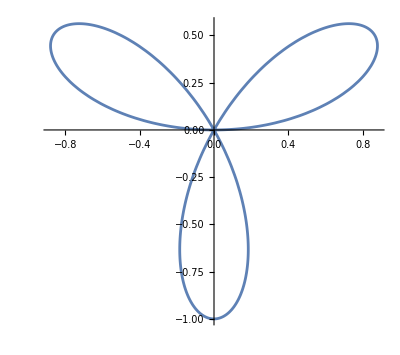

```mathematica
line={Cos[t],Sin[t]}Sin[3t];
ParametricPlot[line,{t,0,π}]
```

```mathematica
s/.{u,v}->line
```

{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}

```mathematica
Thread[{u,v}->line]
```

{u→Cos[t] Sin[3 t],v→Sin[t] Sin[3 t]}

```mathematica
s/.Thread[{u,v}->line]
```

{Cos[Cos[t] Sin[3 t]] Sin[Sin[t] Sin[3 t]],Sin[Cos[t] Sin[3 t]] Sin[Sin[t] Sin[3 t]],Cos[Sin[t] Sin[3 t]]}

```mathematica
lg=ParametricPlot3D[s/.Thread[{u,v}->line],{t,0,π}]
```

-Graphics3D-

```mathematica
l=s/.Thread[{u,v}->(line+π/2)];
lg=ParametricPlot3D[l,{t,0,π}]
```

-Graphics3D-

```mathematica
Show[sg,lg,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
tg=lg/.Line[pts_,rest___]:>Tube[pts,0.02,rest]
```

-Graphics3D-

```mathematica
Show[sg,tg]
```

-Graphics3D-

```mathematica
vs=PolyhedronData["Tetrahedron","Vertices"]
```

{{0,0,√(2/3)-1/(2 √6)},{-1/(2 √3),-1/2,-1/(2 √6)},{-1/(2 √3),1/2,-1/(2 √6)},{1/(√3),0,-1/(2 √6)}}

```mathematica
Norm[vs[[1]]]
Norm[vs[[2]]]
Norm[vs[[3]] √(8/3)]
```

√(2/3)-1/(2 √6)

(√(3/2))/2

1

```mathematica
vs=vs √(8/3);
```

```mathematica
Graphics3D[{{Opacity[0.5],Sphere[]},PointSize[Large],Point[vs]}]
```

-Graphics3D-

```mathematica
v0={0,1,0};
l1=RotationMatrix[{v0,#}].l&/@vs;
```

```mathematica
mtg=ParametricPlot3D[l1,{t,0,π}]/.Line[pts_,rest___]:>Tube[pts,0.03,rest]
```

-Graphics3D-

```mathematica
Show[mtg,Graphics3D[{Opacity[0.8],Sphere[]}]]
```

-Graphics3D-

### 到这里有两个问题 如何使三叶草的尖对齐 三叶草的尖有一个不一样